```mathematica
a2=Import["G:\\calc-online\\gpd\\k-result\\diagram-f-n.wdx"];
f1f=Query[1,1]@a2;
g1f=Query[1,2]@a2;
f2f=Query[2,1]@a2;
g2f=Query[2,2]@a2;
f3f=Query[3,1]@a2;
g3f=Query[3,2]@a2;
f12f=f1f/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
f22f=f2f/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
f32f=f3f/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
g12f=g1f/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
g22f=g2f/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
g32f=g3f/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};

ft1f=f12f/.{Q^2->(-t),Q^4->t^2};
ft2f=f22f/.{Q^2->(-t),Q^4->t^2};
ft3f=f32f/.{Q^2->(-t),Q^4->t^2};
gt1f=g12f/.{Q^2->(-t),Q^4->t^2};
gt2f=g22f/.{Q^2->(-t),Q^4->t^2};
gt3f=g32f/.{Q^2->(-t),Q^4->t^2};
a3=Import["G:\\calc-online\\gpd\\k-result\\diagram-g-n.wdx"];
f1g=Query[1,1]@a3;
g1g=Query[1,2]@a3;
f2g=Query[2,1]@a3;
g2g=Query[2,2]@a3;
f3g=Query[3,1]@a3;
g3g=Query[3,2]@a3;
f12g=f1g/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
f22g=f2g/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
f32g=f3g/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
g12g=g1g/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
g22g=g2g/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
g32g=g3g/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};

ft1g=f12g/.{Q^2->(-t),Q^4->t^2};
ft2g=f22g/.{Q^2->(-t),Q^4->t^2};
ft3g=f32g/.{Q^2->(-t),Q^4->t^2};
gt1g=g12g/.{Q^2->(-t),Q^4->t^2};
gt2g=g22g/.{Q^2->(-t),Q^4->t^2};
gt3g=g32g/.{Q^2->(-t),Q^4->t^2};
```

```mathematica
nf1xf[y_]=Simplify[ft1f/.{MB->0.939,mm->0.1381,MM->0.939,P1->1,Λ->1,t->-1,ξ->0.1}];
nf2xf[y_]=Simplify[ft2f/.{MB->0.939,mm->0.1381,MM->0.939,P1->1,Λ->1,t->-1,ξ->0.1}];
nf3xf[y_]=Simplify[ft3f/.{MB->0.939,mm->0.1381,MM->0.939,P1->1,Λ->1,t->-1,ξ->0.1}];

nf1xg[y_]=Simplify[ft1g/.{MB->0.939,mm->0.1381,MM->0.939,P1->1,Λ->1,t->-1,ξ->0.1}];
nf2xg[y_]=Simplify[ft2g/.{MB->0.939,mm->0.1381,MM->0.939,P1->1,Λ->1,t->-1,ξ->0.1}];
nf3xg[y_]=Simplify[ft3g/.{MB->0.939,mm->0.1381,MM->0.939,P1->1,Λ->1,t->-1,ξ->0.1}];
```

```mathematica
inff[y_]:=NIntegrate[nf1xf[y],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];
infg[y_]:=NIntegrate[nf2xg[y],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];
```

```mathematica
lyff=ParallelTable[{y,inff[y]},{y,-0.2,-0.1,0.001}];
syff=Interpolation[lyff];
```

```mathematica
lyfg=ParallelTable[{ξ,infg[ξ]},{ξ,1,1.1,0.001}];
syfg=Interpolation[lyfg];
```

```mathematica
Plot[I*syff[y],{y,-0.2,0}]
```

-Graphics-

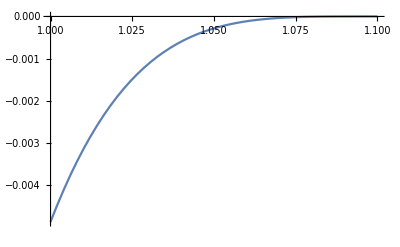

```mathematica
Plot[I*syfg[x],{x,1,1.1}]
```